```mathematica
tsquaredtimesdZdt[t_]:=Sum[(2j+1)*j*(j+1)*Exp[-j*(j+1)/t],{j,0,10}]
```

```mathematica
partitionfunction[t_]:=Sum[(2j+1)*Exp[-j*(j+1)/t],{j,0,10}]
```

```mathematica
energy[t_]:=tsquaredtimesdZdt[t]/partitionfunction[t]
```

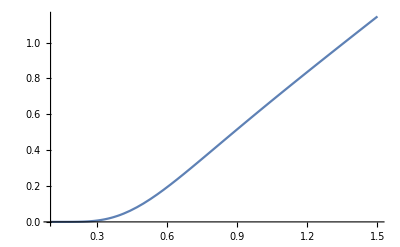

```mathematica
Plot[energy[t],{t,0.1,1.5}]
```

```mathematica
SpecificHeat[t_]:=energy'[t]
```

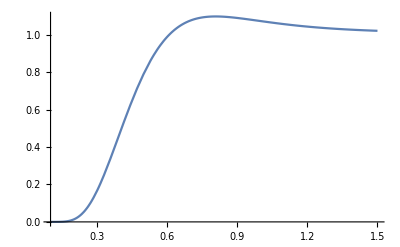

```mathematica
Plot[SpecificHeat[t],{t,0.1,1.5}]
```